### Pregunta 1

#### Parte a

```mathematica
(*Veamos que los graficos se superpongan y sea periodico, sumemos hasta 100 terminos*)
```

```mathematica
f[t_]:= 2/Pi + 4/Pi Sum[(-1)^(n+1)/(4 n^2-1)Cos[2 n t],{n,1,50}]
```

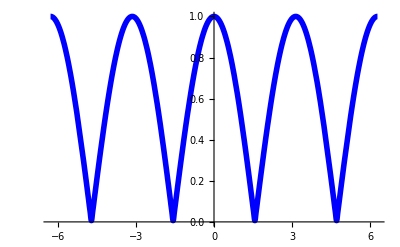

```mathematica
plot1aa = Plot[f[t],{t,-2Pi,2Pi},PlotStyle->{Blue,Thickness[0.01]}]
```

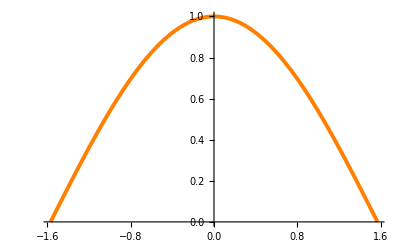

```mathematica
plot1ab = Plot[Cos[t],{t,-Pi/2,Pi/2},PlotStyle->{Orange,Thickness[0.007]}]
```

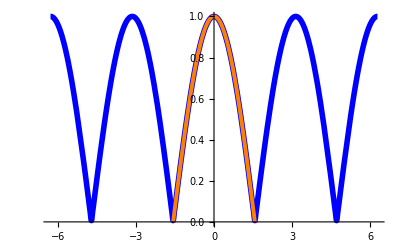

```mathematica
Show[plot1aa,plot1ab](*Es la misma funcion*)
```

#### Parte b

```mathematica
Sum[(-1)^n/(4 n^2-1),{n,1,Infinity}]
```

(2-π)/4

#### Parte c

```mathematica
Sum[1/((4 n^2-1)^2),{n,1,Infinity}]
```

1/16 (-8+π^2)

### Pregunta 2

#### Parte a

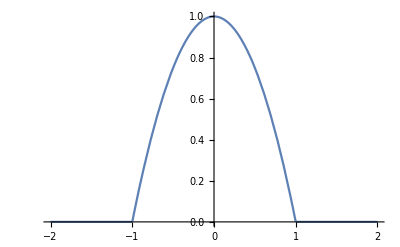

```mathematica
Plot[(1-t^2) (UnitStep[t+1]-UnitStep[t-1]),{t,-2,2},PlotRange->All]
```

```mathematica
FourierTransform[(1-t^2) (UnitStep[t+1]-UnitStep[t-1]),t,w,FourierParameters->{1, -1}]
```

(2 ⅈ ⅇ^(-ⅈ w))/w^3-(2 ⅈ ⅇ^(ⅈ w))/w^3-(2 ⅇ^(-ⅈ w))/w^2-(2 ⅇ^(ⅈ w))/w^2

```mathematica
ExpToTrig[(2 ⅈ ⅇ^(-ⅈ w))/w^3-(2 ⅈ ⅇ^(ⅈ w))/w^3-(2 ⅇ^(-ⅈ w))/w^2-(2 ⅇ^(ⅈ w))/w^2]
```

-(4 Cos[w])/w^2+(4 Sin[w])/w^3

#### Parte b

```mathematica
FourierTransform[(-4 t Cos[t]+4 Sin[t])/t^3,t,w,FourierParameters->{1, -1}]
```

-π (-1+w^2) (Sign[1-w]+Sign[1+w])

```mathematica
(*De nuevo, falta un 2, pero esta ahi al evaluar sign + sign cuando los 2 valen 1, grafiquemos, vemos que la grafica llega hasta 2pi en lugar de 1*)
```

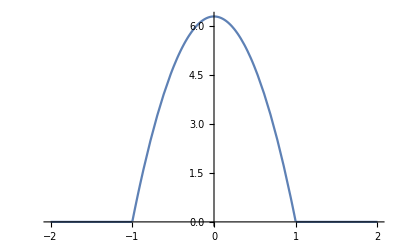

```mathematica
Plot[-π (-1+w^2) (Sign[1-w]+Sign[1+w]),{w,-2,2}]
```

### Pregunta 4

```mathematica
400/Pi^2 Sum[1/n^2,{n,1,Infinity}]
```

200/3

```mathematica
TableForm[Table[{n,400/Pi^2 NSum[1/k^2,{k,1,n}],400/Pi^2 NSum[1/k^2,{k,1,n}]/(200/3)},{n,1,12}],TableHeadings->{None, {"n", "P_n","P_n/P"}}]
```

n | P_n | P_n/P
1 | 40.5285 | 0.607927
2 | 50.6606 | 0.759909
3 | 55.1638 | 0.827456
4 | 57.6968 | 0.865452
5 | 59.3179 | 0.889769
6 | 60.4437 | 0.906656
7 | 61.2708 | 0.919062
8 | 61.9041 | 0.928561
9 | 62.4044 | 0.936067
10 | 62.8097 | 0.942146
11 | 63.1447 | 0.94717
12 | 63.4261 | 0.951392

### Pregunta 5

```mathematica
InverseFourierTransform[1/(w^2+8w+20),w,t,FourierParameters->{1, -1}]
```

1/4 ⅇ^((-2-4 ⅈ) t) (ⅇ^(4 t) HeavisideTheta[-t]+HeavisideTheta[t])

```mathematica
(*Es la manera del Mathemtica de ponerlo en lugar de poner un valor absoluto, pero es +2t en t< 0 lo que esta vivo y -2t en t>0 lo que esta vivo, es igual*)
```

#### Pregunta 6

```mathematica
1/(2Pi)Integrate[4/x^2,{x,1,4}]
```

3/(2 π)